```mathematica
(* RUN transientQBD_functions.nb FIRST !!!! *)
Tinfinite={0,1};
K = 2;

F=ConstantArray[0,K];
B=ConstantArray[0,K];
L=ConstantArray[0,K];
Lv=ConstantArray[0,K+1];

Lv[[1]]={{-lamda}};
F[[1]]=({{0, 0, lamda}});
B[[1]]=({{lamdad}, {0}, {0}});
Lv[[2]]=({{-lamda-lamdad, 0, 0}, {0, -lamda-lamdad, lamdad}, {lamdad, gamma, -gamma-lamdad}});
F[[2]]=({{lamda, 0, 0}, {0, lamda, 0}, {0, 0, 0}});
L[[2]]=({{-lamda-lamdad, 0, 0}, {0, -lamda-lamdad, lamdad}, {lamdad, gamma, -gamma-2lamdad}});
B[[2]]=({{0, 0, lamdad}, {0, 0, 0}, {0, 0, lamdad}});
```

```mathematica
Lv[[1]]+F[[1]].Table[1,{3}]//Chop
B[[1]]+(Lv[[2]]+F[[2]]).Table[1,{3}]//Chop
(B[[2]]+L[[2]]+F[[2]]).Table[1,{3}]//Chop
```

{{0}}

{{0},{0},{0}}

{0,0,0}

```mathematica
e1={1 };
ea={1 , 0, 0};
eb={0 , 1, 0};
t=30;
(*Recurrent NonNull   drift<0*)
{B1,L1,F1,Lv1}={B,L,F,Lv}/.{lamda->0.5,lamdad->1,gamma->0.5};
(* Recurrent Null / Transient Case  drift>0*)
{B2,L2,F2,Lv2}={B,L,F,Lv}/.{lamda->1,lamdad->0.5,gamma->1};
```

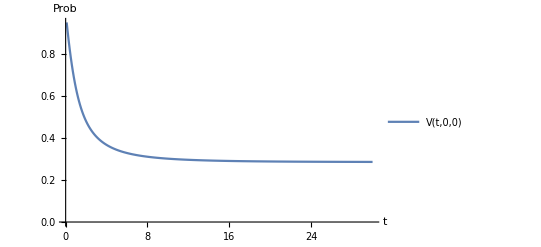

```mathematica
(*figure 4 V(t,0,0)*)res0= ILT[Function[s,Transient2Open[B1,L1,F1,Lv1,Tinfinite,0,0,s]],Range[1/10,t,1/10], 35];
fres0=Table[e1.res0[[i,;;,;;]].e1,{i,1,Dimensions[res0][[1]]}];(* Vall(t,0,0)*)
linexx=Transpose[{Range[1/10,t,1/10],fres0}];
ListLinePlot[linexx,PlotRange->All,PlotLegends->Placed[{"V(t,0,0)"},{Right,Top}],AxesLabel->{"t","Prob"}]
```

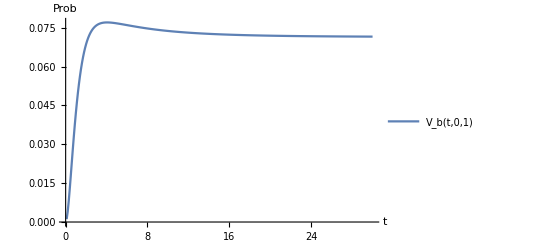

```mathematica
(*  figure 3 vb(t,0,1)*)
res1= ILT[Function[s,Transient2Open[B1,L1,F1,Lv1,Tinfinite,0,1,s]],Range[1/10,t,1/10], 35];
fres1=Table[e1.res1[[i,;;,;;]].eb,{i,1,Dimensions[res1][[1]]}];
linexx1=Transpose[{Range[1/10,t,1/10],fres1}];
ListLinePlot[linexx1,PlotRange->All,PlotLegends->Placed[{"V_b(t,0,1)"},{Right,Top}],AxesLabel->{"t","Prob"}]
```

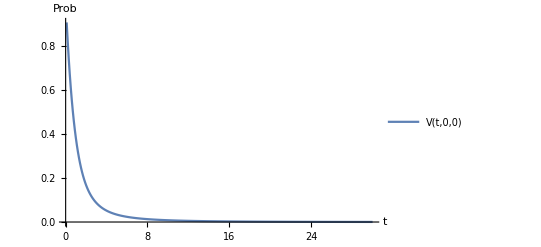

```mathematica
(*  figure 5 V(t,0,0)*)res2= ILT[Function[s,Transient2Open[B2,L2,F2,Lv2,Tinfinite,0,0,s]],Range[1/10,t,1/10], 35];
fres2=Table[e1.res2[[i,;;,;;]].e1,{i,1,Dimensions[res2][[1]]}];
linexx2=Transpose[{Range[1/10,t,1/10],fres2}];
ListLinePlot[linexx2,PlotRange->All,PlotLegends->Placed[{"V(t,0,0)"},{Right,Top}],AxesLabel->{"t","Prob"}]
```

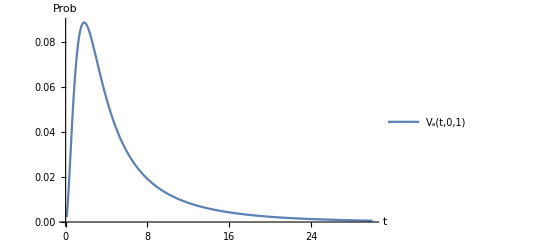

```mathematica
(*  figure 6 va(t,0,1)*)
res3= ILT[Function[s,Transient2Open[B2,L2,F2,Lv2,Tinfinite,0,1,s]],Range[1/10,t,1/10], 35];
fres3=Table[e1.res3[[i,;;,;;]].ea,{i,1,Dimensions[res3][[1]]}];
linexx3=Transpose[{Range[1/10,t,1/10],fres3}];
ListLinePlot[linexx3,PlotRange->All,PlotLegends->Placed[{"V_a(t,0,1)"},{Right,Top}],AxesLabel->{"t","Prob"}]
```

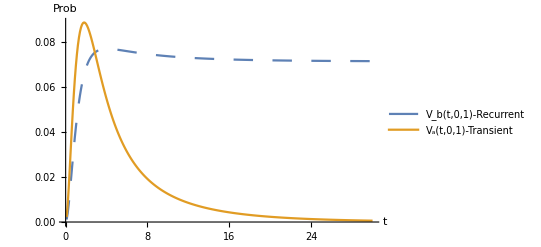

```mathematica
ListLinePlot[{linexx1,linexx3},PlotRange->All,PlotLegends->Placed[{"V_b(t,0,1)-Recurrent","V_a(t,0,1)-Transient"},Center],AxesLabel->{"t","Prob"},PlotStyle -> { Dashing[Large],}]
```

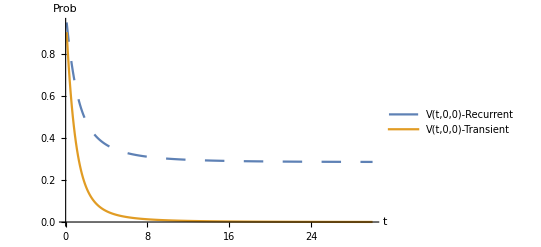

```mathematica
ListLinePlot[{linexx,linexx2},PlotRange->All,PlotLegends->Placed[{"V(t,0,0)-Recurrent","V(t,0,0)-Transient"},{Right,Top}],AxesLabel->{"t","Prob"},PlotStyle -> { Dashing[Large], }]
```